```mathematica
p0[t_]:=(Sin[2Pi t]+1)/2
p1[t_]:=p0[t-1/3]
p2[t_]:=p0[t-2/3]
```

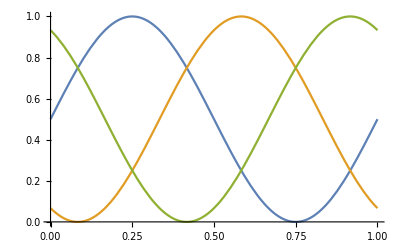

```mathematica
Plot[{p0[t],p1[t],p2[t]},{t,0,1}]
```

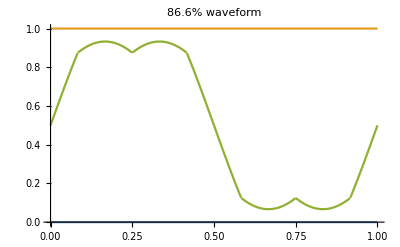

```mathematica
pole0[t_]:=(p0[t]+1/2 -1/2 (Max[p0[t],p1[t],p2[t]]+Min[p0[t],p1[t],p2[t]])); (* Completely stupid name for phase waveform *)
Plot[{0,1,pole0[t]},{t,0,1},PlotLabel->"86.6% waveform"]
```

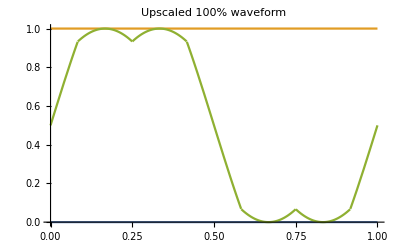

```mathematica
pole0norm=(1/2-Minimize[pole0[t],{t}][[1]]//FullSimplify)*2;
phase0[t_]:=(pole0[t]-1/2)/pole0norm+1/2
Plot[{0,1,phase0[t]},{t,0,1},PlotLabel->"Upscaled 100% waveform"]
```

```mathematica
spaceVectorTable[amplitude_,pointCount_]:=Table[Round[(amplitude phase0[t/pointCount])//N],{t,0,pointCount-1}]
```

{900,923,947,971,994,1018,1041,1065,1088,1111,1135,1157,1181,1204,1226,1249,1272,1295,1317,1340,1362,1384,1406,1427,1449,1471,1491,1513,1534,1555,1575,1582,1588,1595,1601,1607,1612,1617,1622,1627,1633,1637,1641,1646,1649,1653,1656,1660,1662,1665,1667,1670,1672,1673,1675,1677,1678,1679,1679,1679,1679,1679,1679,1679,1678,1677,1675,1673,1672,1670,1667,1665,1662,1660,1656,1653,1649,1646,1641,1637,1633,1627,1622,1617,1612,1607,1601,1595,1588,1582,1575,1582,1588,1595,1601,1607,1612,1617,1622,1627,1633,1637,1641,1646,1649,1653,1656,1660,1662,1665,1667,1670,1672,1673,1675,1677,1678,1679,1679,1679,1679,1679,1679,1679,1678,1677,1675,1673,1672,1670,1667,1665,1662,1660,1656,1653,1649,1646,1641,1637,1633,1627,1622,1617,1612,1607,1601,1595,1588,1582,1575,1555,1534,1513,1491,1471,1449,1427,1406,1384,1362,1340,1317,1295,1272,1249,1226,1204,1181,1157,1135,1111,1088,1065,1041,1018,994,971,947,923,900,877,853,829,806,782,759,735,712,689,665,643,619,596,574,551,528,505,483,460,438,416,394,373,351,329,309,287,266,245,225,218,212,205,199,193,188,183,178,173,167,163,159,154,151,147,144,140,138,135,133,130,128,127,125,123,122,121,121,121,121,121,121,121,122,123,125,127,128,130,133,135,138,140,144,147,151,154,159,163,167,173,178,183,188,193,199,205,212,218,225,218,212,205,199,193,188,183,178,173,167,163,159,154,151,147,144,140,138,135,133,130,128,127,125,123,122,121,121,121,121,121,121,121,122,123,125,127,128,130,133,135,138,140,144,147,151,154,159,163,167,173,178,183,188,193,199,205,212,218,225,245,266,287,309,329,351,373,394,416,438,460,483,505,528,551,574,596,619,643,665,689,712,735,759,782,806,829,853,877}

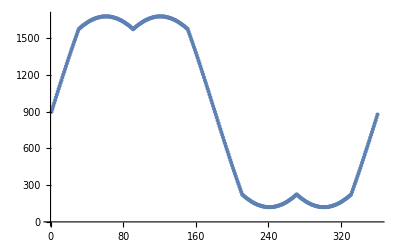

```mathematica
sv1800x360=(spaceVectorTable[1800,360]-900)*Sqrt[3]/2 + 900//Round
ListPlot[sv1800x360]
```

{32768,33758,34748,35738,36727,37714,38700,39684,40666,41646,42623,43597,44568,45535,46498,47457,48411,49361,50306,51245,52179,53107,54028,54943,55852,56753,57647,58534,59412,60283,61145,61427,61699,61964,62219,62465,62702,62930,63149,63359,63559,63750,63931,64103,64266,64418,64562,64695,64819,64933,65037,65132,65216,65291,65355,65410,65455,65490,65515,65530,65535,65530,65515,65490,65455,65410,65355,65291,65216,65132,65037,64933,64819,64695,64562,64418,64266,64103,63931,63750,63559,63359,63149,62930,62702,62465,62219,61964,61699,61427,61145,61427,61699,61964,62219,62465,62702,62930,63149,63359,63559,63750,63931,64103,64266,64418,64562,64695,64819,64933,65037,65132,65216,65291,65355,65410,65455,65490,65515,65530,65535,65530,65515,65490,65455,65410,65355,65291,65216,65132,65037,64933,64819,64695,64562,64418,64266,64103,63931,63750,63559,63359,63149,62930,62702,62465,62219,61964,61699,61427,61145,60283,59412,58534,57647,56753,55852,54943,54028,53107,52179,51245,50306,49361,48411,47457,46498,45535,44568,43597,42623,41646,40666,39684,38700,37714,36727,35738,34748,33758,32768,31777,30787,29797,28808,27821,26835,25851,24869,23889,22912,21938,20967,20000,19037,18078,17124,16174,15229,14290,13356,12428,11507,10592,9683,8782,7888,7001,6123,5252,4390,4108,3836,3571,3316,3070,2833,2605,2386,2176,1976,1785,1604,1432,1269,1117,973,840,716,602,498,403,319,244,180,125,80,45,20,5,0,5,20,45,80,125,180,244,319,403,498,602,716,840,973,1117,1269,1432,1604,1785,1976,2176,2386,2605,2833,3070,3316,3571,3836,4108,4390,4108,3836,3571,3316,3070,2833,2605,2386,2176,1976,1785,1604,1432,1269,1117,973,840,716,602,498,403,319,244,180,125,80,45,20,5,0,5,20,45,80,125,180,244,319,403,498,602,716,840,973,1117,1269,1432,1604,1785,1976,2176,2386,2605,2833,3070,3316,3571,3836,4108,4390,5252,6123,7001,7888,8782,9683,10592,11507,12428,13356,14290,15229,16174,17124,18078,19037,20000,20967,21938,22912,23889,24869,25851,26835,27821,28808,29797,30787,31777}

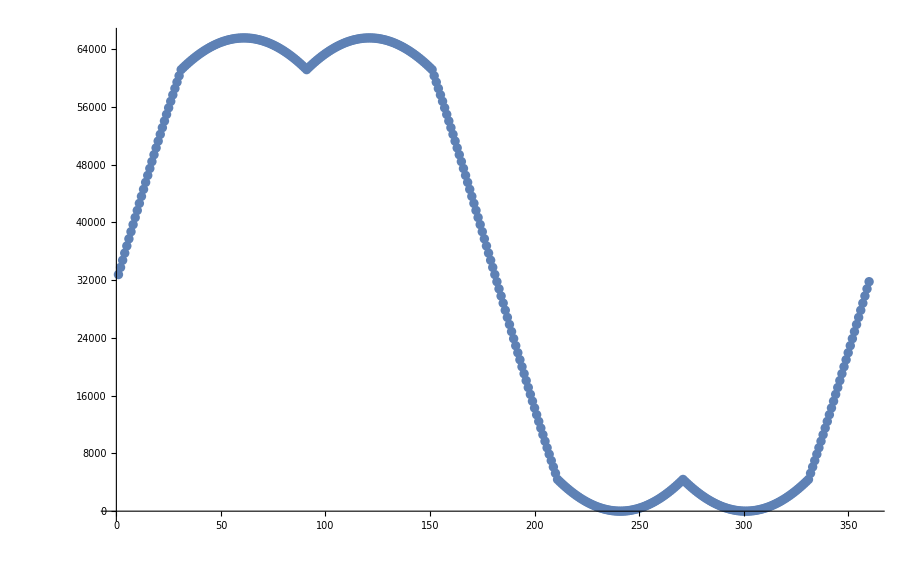

```mathematica
sv2E16x360=spaceVectorTable[65535,360]
ListPlot[sv2E16x360]
```